```mathematica
ClearAll["`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Once[Get["Project2.m","IX1501"]]
```

```mathematica
n = 50;
```

```mathematica
randomSample = randomNumber[0,n];
```

```mathematica
sort = Sort[randomSample]
```

{0.607798,0.746604,0.779027,0.803152,1.09729,1.12253,1.36424,1.43747,1.54323,1.84927,1.89486,1.95643,2.14607,2.15836,2.20919,2.44855,2.93989,2.98494,3.12444,3.22529,3.27709,3.5941,3.63187,3.7148,3.981,4.04971,4.50004,4.65182,5.14819,5.40641,5.47168,5.76248,6.04895,6.15796,6.1729,6.19193,6.77807,6.99019,7.1122,7.71151,7.78145,8.7045,8.83574,9.85421,9.88903,10.9499,11.2957,13.9716,15.2663,17.7602}

```mathematica
Δ=1/n;
pdata=Δ/2+Range[0,1-Δ,Δ]//N;
```

```mathematica
cdf = Transpose[{sort, pdata}];
```

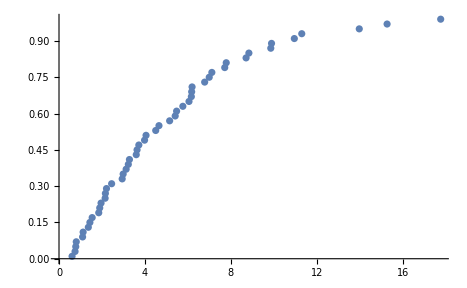

```mathematica
ListPlot[cdf]
```

```mathematica
μ = Mean[sort]
```

5.142

```mathematica
s = StandardDeviation[sort]
```

3.93203

```mathematica
solA = NSolve[Integrate[x*E^(-a*x), {x, 0, ∞}] == μ, a][[1]][[1]][[2]]
```

0.440995

```mathematica
solA
```

0.440995

```mathematica
solA2 =NSolve[Integrate[x*x*E^(-a*x), {x, 0, ∞}] == μ, a, Reals][[1]][[1]][[2]]
```

0.72996

```mathematica
pdf1[x_] := E^(-solA*x)
```

```mathematica
pdf2[x_] = x*E^(-solA2*x)
```

ⅇ^(-0.72996 x) x

```mathematica
pdf3[x_] := x*(x+0)*E^(-0*x)
```

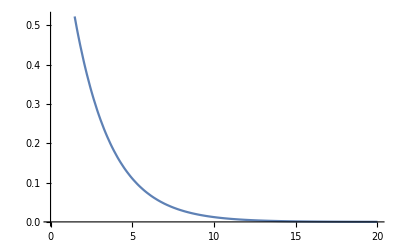

```mathematica
Show[Plot[pdf1[x], {x, 0, 20}]]
```

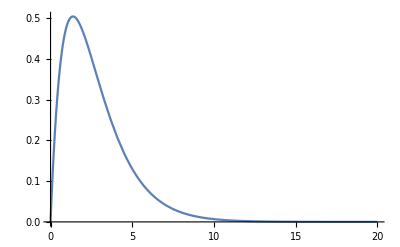

```mathematica
Plot[pdf2[x], {x, 0, 20}]
```

```mathematica
(*NSolve[{Integrate[x^2 * x*(x+b)*E^(-a*x) - (x*x*(x+b)*E^(-a*x))^2, {x, 0, n}]== s^2, Integrate[(x+b)*x*x*E^(-a*x), {x, 0, n}] == μ}, {a,b}]*)
```

```mathematica
listFun1[x_] := pdf1[sort[[x]]]
```

```mathematica
modelList1 = Array[listFun1, n];
```

```mathematica
comparedata1 = Transpose[{modelList1,pdata}];
```

```mathematica
dataplot1=ListPlot[comparedata1,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf", PlotRange->{0, 1}];
```

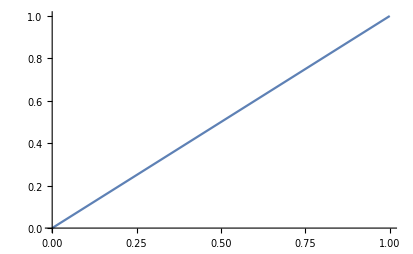

```mathematica
lineplot =Plot[x, {x, 0, 1}]
```

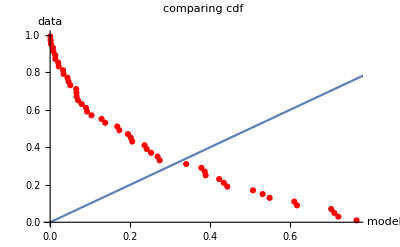

```mathematica
Show[dataplot1,lineplot]
```

```mathematica
listFun2[x_] := pdf2[sort[[x]]]
```

```mathematica
modelList2= Array[listFun2, n];
```

```mathematica
comparedata2 = Transpose[{modelList2,pdata}];
```

```mathematica
dataplot2=ListPlot[comparedata2,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf", PlotRange->{0, 1}];
```

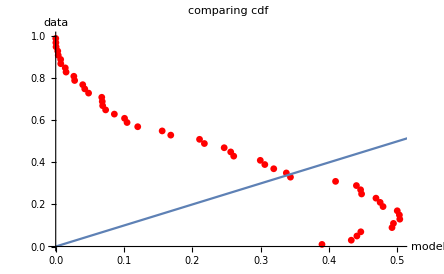

```mathematica
Show[dataplot2,lineplot]
```